# e.All.Numeric.series-o2.recon1.re.sea-valence.strong-only.fch.nb

```mathematica
NotebookFileName[]
```

C:\Users\Tom\Desktop\octet.series.o2.rencon1.strange.sea-valence.strong-only.fch\e.All.Numeric.series-o2.recon1.re.sea-valence.strong-only.fch.nb

```mathematica
Quit[]
```

## note

add the symmetric terms, UUU DDD SSS

for perspective quark, use perspective fucoeandmrrlnm

this nb is to numeric evaluating the Γμs

and draw pictures.

if consider 1/((1+Q^2/Λ^2)^2)→c^2/((1+Q^2/Λ^2)^2) ,c^2=((Λ^2+mπ^2)/Λ^2)^2,then c^2={1.05349 mπ, 1.79549 mKi, 2.0984 mη}

for different particles, use different rencon

## Initial

```mathematica
Quit[]
```

```mathematica
Clear["Global`*"]
```

inital by hand

```mathematica
Once[<<X`]
```

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

```mathematica
Once[choplimit=10^-8];
```

```mathematica
SetOptions[Simplify,TimeConstraint->1]
```

{Assumptions:>$Assumptions,ComplexityFunction→Automatic,ExcludedForms→{1/ϵ,1/ϵ^2,_FermionLine,_DiracMatrix},TimeConstraint→1,TransformationFunctions→Automatic,Trig→True}

## coefficients & mass constants

a 4 component list, contain all, u,d,s

coe list and mass rule list initial

```mathematica
Once[fucoe=Table[0,{k,1,13,1},{i,1,11,1},{i,1,8,1}]];
```

```mathematica
Once[fumass=Table[0,{k,1,13,1},{i,1,11,1},{i,1,8,1}]];
```

coe list and mass rule get

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"/expression-storage.o2/"}]]
```

```mathematica
Once[fucoeandmrrlnm={
FileNameJoin[{Directory[],"fu.coeandmassrrl.consti.all.m"}],
FileNameJoin[{Directory[],"fu.coeandmassrrl.consti.u.m"}],
FileNameJoin[{Directory[],"fu.coeandmassrrl.consti.d.m"}],
FileNameJoin[{Directory[],"fu.coeandmassrrl.consti.s.m"}]
}
];
```

```mathematica
Once[chpt`qfb`quench`coemass=Get[FileNameJoin[{Directory[],"chpt`qfb`quench`coemass.m"}]]];
Once[chpt`qfa`sea`coemass=Get[FileNameJoin[{Directory[],"chpt`qfa`sea`coemass.m"}]]];
Once[chpt`qfa`valence`coemass=Get[FileNameJoin[{Directory[],"chpt`qfa`valence`coemass.m"}]]];
```

```mathematica
Once[
fucoeandmrrlraw=Map[Get,fucoeandmrrlnm,1]
];
```

```mathematica
fucoeandmrrlraw//Dimensions
```

{4,11,8}

```mathematica
Once[
fucoeandmrrl=Join[fucoeandmrrlraw,
Transpose[chpt`qfb`quench`coemass,{2,3,1}],
Transpose[chpt`qfa`valence`coemass,{2,3,1}],
Transpose[chpt`qfa`sea`coemass,{2,3,1}]
]
];
```

```mathematica
fucoeandmrrl//Dimensions
```

{13,11,8}

mass constant

## order

conmo={1Σ,2Neu,3Ξ,4Λ}--{1Σm,2Σ0,3Σp,4pr,5ne,6Ξm,7Ξ0,8Λ}

conmm={1π,2Ki,3η},

conmd={1Δ,2Σs,3Ξs,4Ω}

## assign value

```mathematica
Once[
{conmπ,conmKi,conmη,conmEtas}={
0.1381,
0.4956,
0.5693,
0.9452
}
];
```

```mathematica
Once[
{conmΣ,conmN,conmΞ,conmΛ,conmΛΣ,
conmUUU,conmDDD,conmSSS(* the symmetric terms *)
}={
1.193,0.939,1.315,1.116,1.155,
0.939,0.939,1.315
}
];
```

```mathematica
Once[
{conmΔ,conmΣs,conmΞs,conmΩ}={
1.232,
1.385,
1.530,
1.672
}
];
```

```mathematica
{conmN,conmη,conmΞs}
```

{0.939,0.5693,1.53}

fu Coefficients mass rules reduce

## fu Coefficients

in {4,9} external sign[-]

fusign8, fusign9

fusign9

```mathematica
fucoepresign={
(*+++++++++++++++++++111++++++++++++++++++++++++++++++++++++++*)
{1,1,1,
-1,(*4*)-1,(*5*)
1,1,fusign8,(*8*)fusign9,(*9*)
1,1(*11*)},
(*+++++++++++++++++++222++++++++++++++++++++++++++++++++++++++*)
{1,1,1,
-1,(*4*)-1,(*5*)
1,1,-1,(*8*)-1,(*9*)
1,1(*11*)},
(*+++++++++++++++++++333++++++++++++++++++++++++++++++++++++++*)
{1,1,1,(*3*)
-1,(*4*)-1,(*5*)
1,1,-1,(*8*)-1,(*9*)
1,1(*11*)}(*fch's sign*)
}⟦3⟧;
```

1 for fitting, 2 for calc/test

```mathematica
(*fucoeandmrrlraw [consti,figure,octet][4*11*8]*)
fucoe=Table[
Simplify[
fucoepresign*Values[fucoeandmrrl⟦i⟧]
]
,{i,1,13,1}
];//AbsoluteTiming
```

{1.84565,Null}

## fu mass rules

```mathematica
fumass=Keys[fucoeandmrrl];
```

```mathematica
fucoe//Dimensions
fumass//Dimensions
```

{13,11,8}

{13,11,8}

magnetic momentum tree level

octetmagetonc1={(*1*)-c1/3,(*2*)c1/3,(*3*)c1,(*4*)c1,(*5*)-(2 c1)/3,(*6*)-c1/3,(*7*)-(2 c1)/3,(*8*)-c1/3};

```mathematica
octetmageton={(*1*) −1.160,(*2*) 0.60,(*3*)2.458,
  (*4*)2.7928473446, (*5*)−1.9130427,
  (*6*)−0.6507,(*7*)−1.250,
 (*8*)−0.613};
```

rule lists

```mathematica
Once[constmo={
(*1*)conmΣ,(*2*)conmΣ,(*3*)conmΣ,
(*4*)conmN,(*5*)conmN,
(*6*)conmΞ,(*7*)conmΞ,
(*8*)conmΛ
}
];
```

```mathematica
baselist1={
{mN->conmΣ},{mN->conmΣ},{mN->conmΣ},
{mN->conmN},{mN->conmN},
{mN->conmΞ},{mN->conmΞ},
{mN->conmΛ}
};
```

```mathematica
c3 = c2 - c1;
```

```mathematica
baselist2={
f->0.093,
zi->-1,
di->0.76,fi->0.50,
Λ0->0.80,ci->1.5,
c1->1.7981713337357232,c2->0.5100238092719666
};
```

for neutron pull-apart, best octet fit Λ0≈1~0.1

```mathematica
baselist=Table[
Join[baselist1⟦i⟧,baselist2]
,{i,1,8,1}
];
```

## para test c1c2 sum-square all-baryons

Λ0→0.80,ci→1.5,
{0.124785,{c1→1.79817,c2→0.510024}}

Λ0→0.85,ci→1.5,
{0.124892,{c1→1.73678,c2→0.502641}}

Λ0→0.90,ci→1.5,
{0.126503,{c1→1.67663,c2→0.498392}}

Λ0→1,ci→1.5,
{0.13259,{c1→1.56159,c2→0.498073}}

*********************************************************************

ci→1,Λ0→0.7,
{0.18488,{c1→2.08636,c2→0.534415}}

ci→1,Λ0→0.75,
{0.182312,{c1→2.04853,c2→0.516187}}

ci→1,Λ0→0.8,
{0.182242,{c1→2.01074,c2→0.499423}}

ci→1,Λ0→0.85,
{0.184055,{c1→1.97336,c2→0.484188}}

ci→1,Λ0→0.90,
{0.187237,{c1→1.93672,c2→0.470496}}

ci→1,Λ0→0.95
{0.191372,{c1→1.90108,c2→0.4583}}

ci→1,Λ0→1.0,
{0.196131,{c1→1.86666,c2→0.4475}}

ci→1,Λ0→1.05,
{0.201258,{c1→1.83359,c2→0.437936}}

ci→1,Λ0→1.1,
{0.206563,{c1→1.80199,c2→0.429402}}

**********************************************************************************

ci→1,Λ0→0.90,
{0.187237,{c1→1.93672,c2→0.470496}}

Λ0→0.90,ci→1.05,
{0.180487,{c1→1.9108,c2→0.470493}}

Λ0→0.90,ci→1.1,
{0.17385,{c1→1.88487,c2→0.47114}}

Λ0→0.90,ci→1.15,
{0.16734,{c1→1.85892,c2→0.472429}}

Λ0→0.90,ci→1.2,

{0.160973,{c1→1.83296,c2→0.474349}}

Λ0→0.90,ci→1.25,
{0.154763,{c1→1.80698,c2→0.476887}}

Λ0→0.90,ci→1.3,
{0.148722,{c1→1.78098,c2→0.480032}}

Λ0→0.90,ci→1.35,

{0.142864,{c1→1.75495,c2→0.483769}}

Λ0→0.90,ci→1.40,
{0.137201,{c1→1.72888,c2→0.488085}}

Λ0→0.90,ci→1.45,
{0.131743,{c1→1.70278,c2→0.492964}}

Λ0→0.90,ci→1.5,
{0.126503,{c1→1.67663,c2→0.498392}}

*************************************************************************

Λ0→0.80,ci→1,
{0.182242,{c1→2.01074,c2→0.499423}}

Λ0→0.80,ci→1.05,
{0.176004,{c1→1.99001,c2→0.498533}}

Λ0→0.80,ci→1.1,
{0.169839,{c1→1.96916,c2→0.498082}}

Λ0→0.80,ci→1.15,
{0.163762,{c1→1.94819,c2→0.498068}}

Λ0→0.80,ci→1.2,

{0.157786,{c1→1.92711,c2→0.498491}}

Λ0→0.80,ci→1.25,
{0.151925,{c1→1.90591,c2→0.499347}}

Λ0→0.80,ci→1.3,
{0.146192,{c1→1.88459,c2→0.500634}}

Λ0→0.80,ci→1.35,

{0.140599,{c1→1.86316,c2→0.502349}}

Λ0→0.80,ci→1.40,
{0.13516,{c1→1.84161,c2→0.504489}}

Λ0→0.80,ci→1.45,
{0.129884,{c1→1.81995,c2→0.507049}}

Λ0→0.80,ci→1.5,
{0.124785,{c1→1.79817,c2→0.510024}}

************************************************************

Λ0→0.85,ci→1.5,
{0.124892,{c1→1.73678,c2→0.502641}}

Λ0→1,ci→1.5,
{0.13259,{c1→1.56159,c2→0.498073}}

## para test c1c2 sum - square Nucleon

fch,ci→1,Λ0→0.9,
c1→2.081,c2→0.788,c3→-1.693
{0.0434328,{c1→2.00193}}

ci→1,Λ0→0.8,
 {4.55972×10^-17,{c1→2.14188,c2→0.756261}}

ci→1,Λ0→0.85,
 {6.40949×10^-31,{c1→2.09749,c2→0.752286}}

ci→1,Λ0→0.90,
 {1.33761×10^-17,{c1→2.05739,c2→0.747545}}

ci→1,Λ0→0.95
 {3.9443×10^-31,{c1→2.02149,c2→0.741624}}

ci→1,Λ0→1.0,
 {1.32802×10^-16,{c1→1.98969,c2→0.734099}}

## Γμ get

pure diagram form-factor

```mathematica
Clear[ff1,ff2]
```

```mathematica
Once[Monitor[
ff1=Table[
Get[
FileNameJoin[{Directory[],"f1."<>"analytic."<>ToString[i]<>".m"}]
]
,{i,1,11,1}];
ff2=Table[
Get[
FileNameJoin[{Directory[],"f2."<>"analytic."<>ToString[j]<>".m"}]
]
,{j,1,11,1}];
,{i,j}]//AbsoluteTiming]
```

{4.77098,Null}

```mathematica
ff1//Dimensions
ff2//Dimensions
```

{11}

{11}

form-factor f1, f2

## form-factor list

fucoe=11[diagram]*8[octet]*n(a coefficients lists of n elements)

fumass=11[diagram]*8[octet]*n(n ==above n,n mass rule lists)

diagff=11[diagram]*2[ff1,ff2]*many(contri terms)

```mathematica
fucoe[[2,4]]
```

{((di+fi)^2 (12 mo^2-c1 Q2))/(6 (4 mo^2+Q2)),((di-3 fi)^2 (4 mo^2+c1 Q2))/(6 (4 mo^2+Q2)),((di-fi)^2 (24 mo^2+7 c1 Q2))/(6 (4 mo^2+Q2)),-(c1 (di+3 fi)^2 Q2)/(18 (4 mo^2+Q2)),-(c1 (di-fi) (di+3 fi) Q2)/(3 (4 mo^2+Q2))}

```mathematica
Length[fucoe[[2,4]]]
```

5

contribution combine coefficients,f1, f2

fucoe=11[diagram]*8[octet]*n(coefficients)

fumass=11[diagram]*8[octet]*n(n =above n,mass rule lists)

diagff=11[diagram]*2[ff1,ff2]*many(contri terms)

## convert series to normal

```mathematica
Once[
ff1`series=Transpose[
Table[
{
SeriesCoefficient[ff1⟦diag⟧,0],
SeriesCoefficient[ff1⟦diag⟧,1],
SeriesCoefficient[ff1⟦diag⟧,2]
}
,{diag,1,11,1}
]
,{2,1}
]
];//AbsoluteTiming
```

{0.183805,Null}

```mathematica
Once[
ff2`series=Transpose[(*[oct,loop,consti]8*6*4 transpose into [loop,consti,oct][6*4*8]*)
Table[
{
SeriesCoefficient[ff2⟦diag⟧,0],
SeriesCoefficient[ff2⟦diag⟧,1],
SeriesCoefficient[ff2⟦diag⟧,2]
}
,{diag,1,11,1}
]
,{2,1}
]
];//AbsoluteTiming
```

{0.243669,Null}

```mathematica
Dimensions/@{ff1`series,ff2`series}
```

{{3,11},{3,11}}

## combine fucoe and massrule

```mathematica
Once[nuff1=Table[0,{series,1,3,1},{k,1,13,1}]];
Once[nuff2=Table[0,{series,1,3,1},{k,1,13,1}]];
```

```mathematica
Monitor[
Table[
(nuff1⟦series,constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,diag,oct,coe⟧*ff1`series⟦series,diag⟧
)/.baselist⟦oct⟧
)/.fumass⟦constituent,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{2,3}]);
(nuff2⟦series,constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,diag,oct,coe⟧*ff2`series⟦series,diag⟧
)/.baselist⟦oct⟧
)/.fumass⟦constituent,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{2,3}]);
,{series,1,3,1}(*series order 0 1 2*)
,{constituent,1,13,1}
];
,{series,constituent,oct,diag,coe}
]//AbsoluteTiming
```

{1295.67,Null}

```mathematica
Dimensions/@{nuff1,nuff2}
```

{{3,13,8},{3,13,8}}

```mathematica
(*nuff1,nuff2 is 13*8*)
nugegm=Transpose[(*8*13*2 transpose into 13*8*2*)
Table[
-1/(16 π^2){
nuff1⟦;;,;;,i⟧-Q2/(4 constmo⟦i⟧^2)nuff2⟦;;,;;,i⟧,
nuff1⟦;;,;;,i⟧+nuff2⟦;;,;;,i⟧
}
,{i,1,8,1}]
,{4,1,2,3}
];//AbsoluteTiming
```

{0.0127582,Null}

```mathematica
nugegm//Dimensions
```

{2,3,13,8}

## loopd0d1d2

```mathematica
Once[
octetname=
{"1Σm","2Σ0","3Σp","4pr","5ne" ,"6Ξm","7Ξ0","8Λ"}
];
```

loop derivative coefficient

reciprocal

{loopged0,cur2ereci}
{loopgmd0,cur2mreci}

nugegm⟦f1f2,series,flavor,oct⟧2*3*13*8

```mathematica
({
{loopged0,loopged1,loopged2},
{loopgmd0,loopgmd1,loopgmd2}
}=Simplify[nugegm/.Q2->0]);//AbsoluteTiming
(*{loopged0,loopged1,loopgmd0,loopgmd1} ⟦consti,oct⟧[4,8]*)
```

{0.0302781,Null}

```mathematica
Dimensions/@{loopged0,loopged1,loopged2,loopgmd0,loopgmd1,loopgmd2}
```

{{13,8},{13,8},{13,8},{13,8},{13,8},{13,8}}

## show

```mathematica
TableForm[
Table[
TableForm[
Chop[{loopged0⟦i⟧,loopged1⟦i⟧,loopged2⟦i⟧,cur2ereci⟦i⟧,loopgmd0⟦i⟧,loopgmd1⟦i⟧,loopgmd2⟦i⟧,cur2mreci⟦i⟧}/.Q2->0,choplimit],
TableDepth->2,
TableHeadings->{
{"loopged0","loopged1","loopged2","cur2ereci","loopgmd0","loopgmd1","loopgmd2","cur2mreci"},
octetname
}]
,{i,1,13,1}],
TableDepth->1,
TableSpacing->{3,0},
TableHeadings->{
{
"all","u","d","s",
"u-quench","d-quench","s-quench",
"u-valence","d-valence","s-valence",
"u-sea","d-sea","s-sea"
},
None
}
]
```

all |  | 1Σm | 2Σ0 | 3Σp | 4pr | 5ne | 6Ξm | 7Ξ0 | 8Λ
loopged0 | -0.399988 | 0 | 0.399988 | 0.470298 | 0 | -0.271228 | 0 | 0
loopged1 | 1.42243 | 0.00927804 | -1.40387 | -1.467 | 0.172685 | 0.774968 | -0.0320893 | -0.0190197
loopged2 | -5.32828 | -0.0257996 | 5.27668 | 4.43404 | -1.91221 | -1.68982 | 0.183319 | 0.0254486
cur2ereci | 1.77809 | 0.685901 | 1.75489 | 1.55965 | 2.59565 | 1.42863 | 1.46028 | 0.353523
loopgmd0 | -0.861002 | 0.290658 | 1.44232 | 1.67298 | -1.44115 | -0.232717 | -0.657814 | -0.343914
loopgmd1 | 3.9375 | -0.784224 | -5.50594 | -6.14907 | 5.53256 | 0.634467 | 1.86826 | 0.935454
loopgmd2 | -17.9628 | 1.53334 | 21.0295 | 20.6422 | -19.4529 | -1.30093 | -3.72032 | -1.84784
cur2mreci | 2.28658 | 1.34905 | 1.90871 | 1.83776 | 1.91949 | 1.36317 | 1.42005 | 1.36001
u |  | 1Σm | 2Σ0 | 3Σp | 4pr | 5ne | 6Ξm | 7Ξ0 | 8Λ
loopged0 | 0 | 0.399988 | 0.799976 | 0.940595 | 0.470298 | 0 | 0.271228 | 0.356431
loopged1 | 0.349616 | -1.06353 | -2.47668 | -2.76141 | -1.12172 | 0.0569258 | -0.750131 | -0.977861
loopged2 | -3.27201 | 2.03047 | 7.33294 | 6.94952 | 0.603277 | -0.321433 | 1.55171 | 1.86895
cur2ereci | 1.99011 | 1.32946 | 1.54797 | 1.46791 | 1.19257 | 1.35471 | 1.38284 | 1.37174
loopgmd0 | -0.705091 | 0.44657 | 1.59823 | 1.86685 | -1.24728 | -0.110341 | -0.535438 | -0.183951
loopgmd1 | 3.53752 | -1.1842 | -5.90592 | -6.65179 | 5.02984 | 0.327763 | 1.56155 | 0.532192
loopgmd2 | -17.2118 | 2.28441 | 21.7806 | 21.5932 | -18.5019 | -0.729842 | -3.14923 | -1.0954
cur2mreci | 2.50856 | 1.32588 | 1.84764 | 1.78156 | 2.01632 | 1.48522 | 1.4582 | 1.44656
d |  | 1Σm | 2Σ0 | 3Σp | 4pr | 5ne | 6Ξm | 7Ξ0 | 8Λ
loopged0 | 0.799976 | 0.399988 | 0 | 0.470298 | 0.940595 | 0.271228 | 0 | 0.356431
loopged1 | -2.47668 | -1.06353 | 0.349616 | -1.12172 | -2.76141 | -0.750131 | 0.0569258 | -0.977861
loopged2 | 7.33294 | 2.03047 | -3.27201 | 0.603277 | 6.94952 | 1.55171 | -0.321433 | 1.86895
cur2ereci | 1.54797 | 1.32946 | 1.99011 | 1.19257 | 1.46791 | 1.38284 | 1.35471 | 1.37174
loopgmd0 | 1.59823 | 0.44657 | -0.705091 | -1.24728 | 1.86685 | -0.535438 | -0.110341 | -0.183951
loopgmd1 | -5.90592 | -1.1842 | 3.53752 | 5.02984 | -6.65179 | 1.56155 | 0.327763 | 0.532192
loopgmd2 | 21.7806 | 2.28441 | -17.2118 | -18.5019 | 21.5932 | -3.14923 | -0.729842 | -1.0954
cur2mreci | 1.84764 | 1.32588 | 2.50856 | 2.01632 | 1.78156 | 1.4582 | 1.48522 | 1.44656
s |  | 1Σm | 2Σ0 | 3Σp | 4pr | 5ne | 6Ξm | 7Ξ0 | 8Λ
loopged0 | 0.399988 | 0.399988 | 0.399988 | 0 | 0 | 0.542455 | 0.542455 | 0.356431
loopged1 | -1.09137 | -1.09137 | -1.09137 | -0.0000903287 | -0.0000903287 | -1.46092 | -1.46092 | -0.920802
loopged2 | 2.10786 | 2.10786 | 2.10786 | -0.00634612 | -0.00634612 | 2.87489 | 2.87489 | 1.7926
cur2ereci | 1.36425 | 1.36425 | 1.36425 | -17.5639 | -17.5639 | 1.34658 | 1.34658 | 1.2917
loopgmd0 | -0.425405 | -0.425405 | -0.425405 | -0.0379531 | -0.0379531 | 1.01291 | 1.01291 | 0.847792
loopgmd1 | 1.16847 | 1.16847 | 1.16847 | 0.113781 | 0.113781 | -2.80943 | -2.80943 | -2.27417
loopgmd2 | -2.31561 | -2.31561 | -2.31561 | -0.238394 | -0.238394 | 5.59234 | 5.59234 | 4.44812
cur2mreci | 1.37337 | 1.37337 | 1.37337 | 1.49896 | 1.49896 | 1.38681 | 1.38681 | 1.34123
u-quench |  | 1Σm | 2Σ0 | 3Σp | 4pr | 5ne | 6Ξm | 7Ξ0 | 8Λ
loopged0 | 0 | 0.28364 | 0.462608 | 0.492018 | 0.101142 | 0 | 0.305299 | 0.259486
loopged1 | 0 | -0.48494 | -1.22857 | -1.29423 | -0.383154 | 0 | -0.864233 | -0.716715
loopged2 | 0 | -0.32477 | 2.34881 | 3.10831 | 0.186161 | 0 | 1.66883 | 1.33781
cur2ereci | Indeterminate | 0.854852 | 1.32787 | 1.31523 | 1.89414 | Indeterminate | 1.41539 | 1.38103
loopgmd0 | 0 | 0.122115 | 0.662503 | 1.6894 | -1.435 | 0 | -0.581719 | -0.339115
loopgmd1 | 0 | 0.774847 | -1.72364 | -5.12263 | 4.45808 | 0 | 1.54097 | 1.28873
loopgmd2 | 0 | -6.824 | 3.28987 | 13.8103 | -12.5496 | 0 | -2.98255 | -4.1441
cur2mreci | Indeterminate | -3.17261 | 1.30085 | 1.51611 | 1.55334 | Indeterminate | 1.32449 | 1.90014
d-quench |  | 1Σm | 2Σ0 | 3Σp | 4pr | 5ne | 6Ξm | 7Ξ0 | 8Λ
loopged0 | -0.306532 | 0.0148131 | 0 | 0.588244 | 0.0298464 | -0.00454432 | 0 | 0.142935
loopged1 | 0.891563 | -0.302406 | 0 | -1.76597 | 0.0605281 | 0.0141724 | 0 | -0.424053
loopged2 | -1.76216 | 1.83787 | 0 | 2.91447 | 0.407454 | -0.0479174 | 0 | 0.891603
cur2ereci | 1.45427 | 10.2074 | Indeterminate | 1.50106 | -1.01399 | 1.55936 | Indeterminate | 1.48338
loopgmd0 | -0.0304866 | 0.306683 | 0 | -1.503 | 1.07046 | -0.34409 | 0 | 0.156498
loopgmd1 | 0.0300198 | -1.8738 | 0 | 4.60759 | -3.56547 | 0.945743 | 0 | -0.864929
loopgmd2 | 0.00863407 | 8.91046 | 0 | -12.8101 | 10.899 | -1.87295 | 0 | 3.37968
cur2mreci | 0.492344 | 3.05494 | Indeterminate | 1.5328 | 1.66539 | 1.37427 | Indeterminate | 2.76338
s-quench |  | 1Σm | 2Σ0 | 3Σp | 4pr | 5ne | 6Ξm | 7Ξ0 | 8Λ
loopged0 | -0.105734 | 0.157717 | 0.280321 | 0 | 0 | 0.0076332 | 0.230335 | 0.10857
loopged1 | 0.257945 | -0.428062 | -0.764154 | 0 | 0 | -0.0170303 | -0.586708 | -0.260474
loopged2 | -0.474167 | 0.809256 | 1.46737 | 0 | 0 | 0.0502136 | 1.12214 | 0.472853
cur2ereci | 1.21978 | 1.35706 | 1.363 | Indeterminate | Indeterminate | 1.11554 | 1.2736 | 1.19957
loopgmd0 | -0.212204 | -0.0874232 | -0.322374 | 0 | 0 | 0.438238 | 0.692594 | 0.0834554
loopgmd1 | 0.584534 | 0.240238 | 0.844312 | 0 | 0 | -1.17769 | -1.81466 | -0.206346
loopgmd2 | -1.15888 | -0.48305 | -1.63202 | 0 | 0 | 2.30208 | 3.48896 | 0.381861
cur2mreci | 1.37729 | 1.374 | 1.30952 | Indeterminate | Indeterminate | 1.34366 | 1.31004 | 1.23627
u-valence |  | 1Σm | 2Σ0 | 3Σp | 4pr | 5ne | 6Ξm | 7Ξ0 | 8Λ
loopged0 | 0 | 0.286769 | 0.620979 | 0.660505 | 0.604504 | 0 | 0.177878 | 0.238574
loopged1 | 0 | -1.27344 | -2.16182 | -2.22038 | -1.69893 | 0 | -0.522789 | -0.695975
loopged2 | 0 | 5.54093 | 7.42601 | 6.27579 | 3.48649 | 0 | 1.19971 | 1.44551
cur2ereci | Indeterminate | 2.22033 | 1.74065 | 1.68082 | 1.40522 | Indeterminate | 1.46952 | 1.45861
loopgmd0 | 0 | 0.851075 | 1.46252 | 0.820501 | 0.141971 | 0 | -0.0637271 | 0.0238058
loopgmd1 | 0 | -4.45403 | -6.2522 | -3.8463 | -0.219779 | 0 | 0.244157 | -0.201385
loopgmd2 | 0 | 21.3557 | 25.9211 | 15.7599 | 0.0029978 | 0 | -0.586926 | 0.943196
cur2mreci | Indeterminate | 2.61671 | 2.13748 | 2.34387 | 0.774027 | Indeterminate | 1.91565 | 4.22974
d-valence |  | 1Σm | 2Σ0 | 3Σp | 4pr | 5ne | 6Ξm | 7Ξ0 | 8Λ
loopged0 | 1.03139 | 0.421182 | 0 | 0.315567 | 0.941132 | 0.352165 | 0 | 0.325433
loopged1 | -3.27924 | -1.06395 | 0 | -0.897703 | -3.01066 | -1.01167 | 0 | -0.93439
loopged2 | 9.57854 | 1.72208 | 0 | 1.91956 | 7.82052 | 2.1506 | 0 | 1.86531
cur2ereci | 1.58973 | 1.26305 | Indeterminate | 1.42237 | 1.59949 | 1.43635 | Indeterminate | 1.43561
loopgmd0 | 0.923886 | -0.0794858 | 0 | -0.0602616 | 0.186531 | -0.359571 | 0 | -0.722798
loopgmd1 | -4.91751 | 0.193506 | 0 | 0.28998 | -2.2854 | 0.982101 | 0 | 2.44697
loopgmd2 | 23.4461 | -0.754819 | 0 | -0.95178 | 12.8682 | -1.95981 | 0 | -6.96117
cur2mreci | 2.66132 | 1.21723 | Indeterminate | 2.40601 | 6.12605 | 1.36566 | Indeterminate | 1.6927
s-valence |  | 1Σm | 2Σ0 | 3Σp | 4pr | 5ne | 6Ξm | 7Ξ0 | 8Λ
loopged0 | 0.51251 | 0.310553 | 0.229799 | 0 | 0 | 0.543578 | 0.398339 | 0.242186
loopged1 | -1.38368 | -0.860682 | -0.646976 | 0 | 0 | -1.47381 | -1.10958 | -0.684199
loopged2 | 2.66902 | 1.69345 | 1.27815 | 0 | 0 | 2.89703 | 2.21715 | 1.39788
cur2ereci | 1.34991 | 1.38572 | 1.4077 | Indeterminate | Indeterminate | 1.35566 | 1.39276 | 1.41255
loopgmd0 | -0.166396 | -0.311733 | -0.107309 | 0 | 0 | 0.890853 | 0.688321 | 0.822498
loopgmd1 | 0.426069 | 0.824349 | 0.285715 | 0 | 0 | -2.44269 | -1.93615 | -2.23188
loopgmd2 | -0.809797 | -1.59109 | -0.55312 | 0 | 0 | 4.82829 | 3.88501 | 4.39094
cur2mreci | 1.28029 | 1.32221 | 1.33128 | Indeterminate | Indeterminate | 1.37099 | 1.40643 | 1.35677
u-sea |  | 1Σm | 2Σ0 | 3Σp | 4pr | 5ne | 6Ξm | 7Ξ0 | 8Λ
loopged0 | 0 | -0.00562517 | -0.0889176 | 0.0276349 | 0.22833 | 0 | -0.0120603 | 0.0669424
loopged1 | 0.349481 | 0.23636 | 0.380015 | 0.0703152 | -0.456883 | 0.0566811 | 0.0687289 | -0.18129
loopged2 | -3.27157 | -2.29243 | -1.40659 | -1.0773 | -0.205393 | -0.320751 | -0.204327 | 0.314231
cur2ereci | 1.99083 | 2.18837 | 2.1369 | -1.27222 | 1.00049 | 1.35804 | 2.84938 | 1.35407
loopgmd0 | -0.686117 | -0.425474 | -0.258068 | -0.317382 | -0.192417 | -0.0921162 | -0.0171842 | 0.0446347
loopgmd1 | 3.49023 | 2.24101 | 1.39531 | 1.50013 | 1.3502 | 0.282636 | 0.0956948 | -0.341744
loopgmd2 | -17.1238 | -11.7733 | -6.17227 | -6.44889 | -6.96765 | -0.646125 | -0.175375 | 1.70855
cur2mreci | 2.54347 | 2.63354 | 2.70337 | 2.36329 | 3.50852 | 1.53413 | 2.78438 | 3.82823
d-sea |  | 1Σm | 2Σ0 | 3Σp | 4pr | 5ne | 6Ξm | 7Ξ0 | 8Λ
loopged0 | 0.269816 | 0.128788 | 0 | 0.0301649 | 0.209179 | 0.123496 | 0 | 0.0966351
loopged1 | -0.617832 | -0.152681 | 0.350582 | 0.129863 | -0.476031 | -0.318622 | 0.058679 | -0.228509
loopged2 | 0.532386 | -0.647758 | -3.27518 | -1.38316 | 0.0210749 | 0.554944 | -0.326321 | 0.320365
cur2ereci | 1.14491 | -0.907959 | 1.98495 | -2.15255 | 1.13785 | 1.29001 | 1.3316 | 1.18233
loopgmd0 | -0.381404 | -0.434407 | -0.841013 | -0.339661 | -0.546541 | -0.256527 | -0.2409 | -0.19944
loopgmd1 | 1.6917 | 2.12753 | 3.8763 | 1.72598 | 2.05664 | 0.693025 | 0.651036 | 0.388086
loopgmd2 | -6.71439 | -8.90544 | -17.8418 | -7.67552 | -7.47322 | -1.28685 | -1.32956 | -0.182721
cur2mreci | 2.21773 | 2.44878 | 2.30454 | 2.54074 | 1.8815 | 1.35078 | 1.35126 | 0.972938
s-sea |  | 1Σm | 2Σ0 | 3Σp | 4pr | 5ne | 6Ξm | 7Ξ0 | 8Λ
loopged0 | 0.0866915 | 0.0251967 | -0.0166526 | 0 | 0 | 0.0769043 | -0.000557557 | 0.014444
loopged1 | -0.225847 | -0.0628391 | 0.0595475 | -0.000153472 | -0.000153472 | -0.196421 | 0.00902059 | 0.000143271
loopged2 | 0.416567 | 0.108713 | -0.134094 | -0.00612743 | -0.00612743 | 0.360016 | -0.0320358 | -0.0316966
cur2ereci | 1.30259 | 1.24697 | 1.78793 | -9.9812 | -9.9812 | 1.27705 | 8.08938 | -0.00495953
loopgmd0 | -0.0330723 | -0.0125168 | 0.0180101 | -0.0262101 | -0.0262101 | 0.0111479 | -0.0406764 | 0.136949
loopgmd1 | 0.11704 | 0.0630555 | -0.00238401 | 0.0846446 | 0.0846446 | -0.00123677 | 0.129192 | -0.31894
loopgmd2 | -0.266273 | -0.160817 | -0.049813 | -0.184287 | -0.184287 | -0.0299722 | -0.273576 | 0.571667
cur2mreci | 1.76946 | 2.51884 | 0.0661855 | 1.61473 | 1.61473 | 0.0554712 | 1.58805 | 1.16445

## loop parameters

formfactor parameterization

gm[Q2]=gm0 1/(cur2mre*Q2+1)^2

loopgmd0=gm0

loopgmd1=-2 cur2mre gm0

loopgmd2=6 cur2mre^2 gm0

ge[Q2]=(A Q2)/(1+B Q2)1/(1+cur2ereci*Q2)^2

loopged0==0

loopged1==A

loopged2==2 A (-B-2 cur2ere)

zero waves

## ge

1total:{1,2},{1,5},{1,7},{1,8}

2u-loop :{2,1}, | {2,6}

3d-loop :{3,3}, | {3,7}

4s-loop :{4,4} | ,{4,5}

11u-sea :{11,1} | ,{11,2},{11,6}

12d-sea :{12,2} | ,{12,3},{12,7}

13s-sea :{13,4} | ,{13,5}

## gm none only sign problem

1total:

2u-loop :

3d-loop :

4s-loop :

zero total

## ge

5u-quench :{5,1} | ,{5,6}

6d-quench :{6,3} | ,{6,7}

7s-quench :{7,4} | ,{7,5}

8u-valence :{8,1} | ,{8,6}

9d-valence :{9,3} | ,{9,7}

10s-valence :{10,4} | ,{10,5}

## gm

5u-quench :{5,1} | ,{5,6}

6d-quench :{6,3} | ,{6,7}

7s-quench :{7,4} | ,{7,5}

8u-valence :{8,1} | ,{8,6}

9d-valence :{9,3} | ,{9,7}

10s-valence :{10,4} | ,{10,5}

calc

```mathematica
Once[{cur2ereci,cur2mreci}=Table[Indeterminate,{gegm,1,2,1},{flavor,1,13,1},{octet,1,8,1}]];
```

## cur2ereci

```mathematica
(*=============================cur2ereci dipole==========================================================*)
Table[
cur2ereci⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧=loopged1⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧/(-2loopged0⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧)
,{
flavor`oct (*cycling variable *)
,DeleteCases[(*delete the zero cases*)
Flatten[Table[{i,j},{i,1,13,1},{j,1,8,1}],1],
Alternatives[
{1,2},{1,5},{1,7},{1,8},
{2,1},{2,6},
{3,3},{3,7},
{4,4},{4,5},
{5,1},{5,6},
{6,3},{6,7},
{7,4},{7,5},
{8,1},{8,6},
{9,3},{9,7},
{10,4},{10,5},
{11,1},{11,2},{11,6},
{12,2},{12,3},{12,7},
{13,4},{13,5}
]
]
}
];
```

## cur2ereci zero wave

```mathematica
(*=============================cur2ereci zero wave========================================================*)
Table[
(cur2ereci⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧=(loopged2⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧/(-4loopged1⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧)-loopged1⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧)),
{
flavor`oct,
{
{1,2},{1,5},{1,7},{1,8},
{2,1},{2,6},
{3,3},{3,7},
{4,4},{4,5},
{11,1},{11,2},{11,6},
{12,2},{12,3},{12,7},
{13,4},{13,5}
}
}
(*consti:1all,2u,3d,4s,octet*)
];
(*{cur2ereci,cur2mreci} are ⟦consti,oct⟧[4,8]*)
```

## cur2mreci

```mathematica
(*=============================cur2mreci dipole==========================================================*)
Table[
cur2mreci⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧=loopgmd1⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧/(-2loopgmd0⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧)
,{
flavor`oct (*cycling variable *)
,DeleteCases[(*delete the zero cases*)
Flatten[Table[{i,j},{i,1,13,1},{j,1,8,1}],1],
Alternatives[
{5,1},{5,6},
{6,3},{6,7},
{7,4},{7,5},
{8,1},{8,6},
{9,3},{9,7},
{10,4},{10,5}
]
]
}
];
```

## ge neutral&gm neutral

```mathematica
1:2,5,7,8
```

```mathematica
2:1,6
```

```mathematica
3:3,7
```

```mathematica
4:4,5
```

==========================================GM=====================================

```mathematica
1:2,5,7,8
```

```mathematica
2:1,6
```

```mathematica
3:3,7
```

```mathematica
4:4,5
```

loopgegm[Q2]

```mathematica
(*loopged0,loopged1,loopgmd0,loopgmd1,all is ⟦consti,oct⟧[4,8]*)
(*{cur2ereci,cur2mreci} are ⟦consti,oct⟧[4,8]*)
```

```mathematica
Once[loopgegm=Table[0,{i,1,13,1},{j,1,8,1},{k,1,2,1}]];
```

```mathematica
(*============================= ge dipole==========================================================*)
Table[
loopgegm⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧,1⟧=loopged0⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧*1/(Q2*Abs[cur2ereci⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧]+1)^2
,{
flavor`oct,
DeleteCases[(*delete the zero cases*)
Flatten[
Table[{i,j},{i,1,13,1},{j,1,8,1}]
,1
],
Alternatives[
{1,2},{1,5},{1,7},{1,8},
{2,1},{2,6},
{3,3},{3,7},
{4,4},{4,5},
{5,1},{5,6},
{6,3},{6,7},
{7,4},{7,5},
{8,1},{8,6},
{9,3},{9,7},
{10,4},{10,5},
{11,1},{11,2},{11,6},
{12,2},{12,3},{12,7},
{13,4},{13,5}
]
]
}
];
```

```mathematica
(*=============================ge zero wave==========================================================*)

Table[
loopgegm⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧,1⟧=(loopged1⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧*Q2)/(1+2*loopged1⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧*Q2)^2 1/(1+Abs[cur2ereci⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧]*Q2)^2,
{
flavor`oct,{
{1,2},{1,5},{1,7},{1,8},
{2,1},{2,6},
{3,3},{3,7},
{4,4},{4,5},
{11,1},{11,2},{11,6},
{12,2},{12,3},{12,7},
{13,4},{13,5}
}
}
];
```

```mathematica
(*=============================gm dipole==========================================================*)
Table[
loopgegm⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧,2⟧=loopgmd0⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧*1/(Q2*Abs[cur2mreci⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧]+1)^2
,{
flavor`oct,
DeleteCases[(*delete the zero cases*)
Flatten[
Table[{i,j},{i,1,13,1},{j,1,8,1}]
,1
],
Alternatives[
{5,1},{5,6},
{6,3},{6,7},
{7,4},{7,5},
{8,1},{8,6},
{9,3},{9,7},
{10,4},{10,5}
]
]
}
];
```

```mathematica
(*============================= gm pole==========================================================*)
Table[
loopgegm⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧,2⟧=0,
{
flavor`oct,
{
{5,1},{5,6},
{6,3},{6,7},
{7,4},{7,5},
{8,1},{8,6},
{9,3},{9,7},
{10,4},{10,5}
}
}
];
```

## tree level contributions

initial

because history reasons, all mass mo here is marked as mN

{(c1 Q2)/(3 (4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)+(c1 Q2)/(√3 (4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2), (4 c1 mN^2)/(3(4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)+(4 c1 mN^2)/(√3(4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)},(*2,Σ0*)

{(c1 Q2)/(3 (4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2), (4 c1 mN^2)/(3(4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)},(*2,Σ0*)

```mathematica
Once[
trf1f2={
(*+++++++++++++++++total++++++++++++++++++++++++*)
{{((-12 mo^2+(c1-3 (1+c2)) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},{(c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c2) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}(*Σ*),
{((12 mo^2+(3+c1+3 c2) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},{-(2 c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),-(8 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},(*N*)
{((-12 mo^2+(c1-3 (1+c2)) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},{-(2 c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),-(8 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},
{-(c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),-(4 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}},
(*+++++++++++++++++u++++++++++++++++++++++++*)
{
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+(1+c1+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c3) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c3) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}
},
(*+++++++++++++++++d++++++++++++++++++++++++*)
{
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+(1+c1+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c3) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c3) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}
},
(*+++++++++++++++++s++++++++++++++++++++++++*)
{{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+4 c1+3 c3) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (4 c1+3 c3) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}}
}/.mo->mN
];
(*trf1f2 is [consti,octet,treef1f2][4*8*2]*)
```

gegm

-I el(4 mN^2+c1 Q2)/(4 mN^2+Q2) ,--el/(2mN)(4 (c1-1) mN^2)/(4 mN^2+Q2)

netrf1f2⟦4⟧={(4 mN^2+c1 Q2)/(4 mN^2+Q2)Λ^4/((Λ^2+Q2)^2),(4 (c1-1) mN^2)/(4 mN^2+Q2)Λ^4/((Λ^2+Q2)^2)}/.baselist

```mathematica
(*trf1f2 is [consti,octet,treef1f2][4*8*2]*)
```

```mathematica
Once[
trgegm=Transpose[
Table[
Simplify[
{
trf1f2⟦;;,i,1⟧-Q2/(4 constmo⟦i⟧^2)trf1f2⟦;;,i,2⟧,
trf1f2⟦;;,i,1⟧+trf1f2⟦;;,i,2⟧
}/.baselist⟦i⟧
]
,{i,1,8,1}]
,{2,3,1}]
];//AbsoluteTiming
(*trgegm is [consti,octet,treegegem][4*8*2]*)
```

{0.0355031,Null}

```mathematica
trgegm//Dimensions
```

{4,8,2}

plot

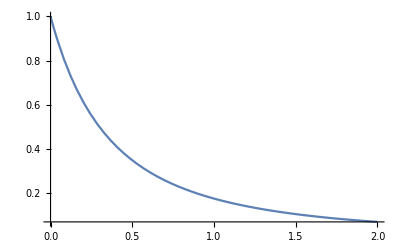

```mathematica
Plot[
trgegm⟦4,1⟧
,{Q2,0.,2.},PlotRange->Full
]
```

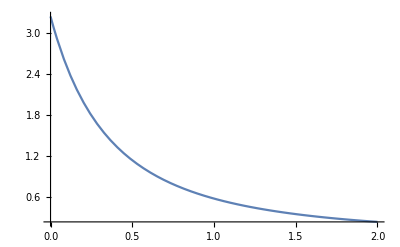

```mathematica
Plot[
trgegm⟦4,2⟧
,{Q2,0.,2.},PlotRange->Full
]
```

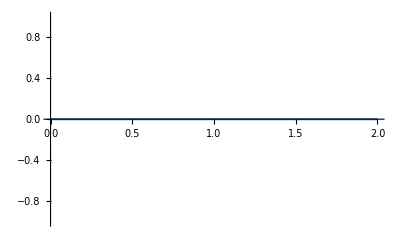

```mathematica
Plot[
trgegm⟦5,1⟧
,{Q2,0.,2.},PlotRange->Full]
```

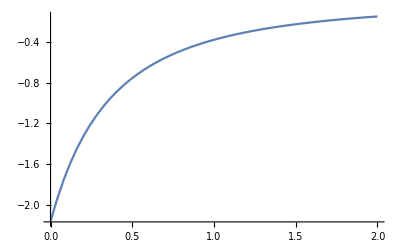

```mathematica
Plot[
trgegm⟦5,2⟧
,{Q2,0.,2.},PlotRange->Full]
```

## rencon calc

constants

octetmagetonc1={(*1*)-c1/3,(*2*)c1/3,(*3*)c1,(*4*)c1,(*5*)-(2 c1)/3,(*6*)-c1/3,(*7*)-(2 c1)/3,(*8*)-c1/3};

```mathematica
Once[
octetcharge={
(*1*)-1,(*2*)0,(*3*)1,
(*4*)1,(*5*)0,
(*6*)-1,(*7*)0,
(*8*)0
}
];
```

```mathematica
Once[
octetmageton={(*1*) −1.160,(*2*) 0.60,(*3*)2.458,
  (*4*)2.7928473446, (*5*)−1.9130427,
  (*6*)−0.6507,(*7*)−1.250,
 (*8*)−0.613}
 ];
```

rencon1

```mathematica
(*trgegm is [consti,octet,treegegem][4*8*2]*)
(*loopged0,loopgmd0 is ⟦consti,oct⟧[4,8]*)
```

```mathematica
rencon=Table[1,{consti,1,4,1},{octet,1,8,1}];
(*+++++++++++++++++renormalized according to charge+++++++++++++*)
Table[
rencon⟦;;,i⟧=
Re[octetcharge⟦i⟧/(
(trf1f2⟦1,i,1⟧/.Q2->0)+
(Cancel[Chop[loopged0⟦1,i⟧,choplimit]]/.{Q2->0})
)]
,{i,{1,3,4,6}}];
(*+++++++++++++++renormalized isospin+++++++++++++++++++++*)
rencon⟦;;,2⟧=rencon⟦;;,3⟧;
rencon⟦;;,5⟧=rencon⟦;;,4⟧;
rencon⟦;;,7⟧=rencon⟦;;,6⟧;
rencon⟦;;,8⟧=Re[1/(1+(
Cancel[Chop[loopged0⟦2,8⟧,choplimit]]/.{Q2->0}
))];
(*++++++++++++++++++++no renormalized+++++++++++++++++++++*)
(*rencon⟦2,1⟧=1;
rencon⟦2,6⟧=1;
rencon⟦3,3⟧=1;
rencon⟦3,7⟧=1;
rencon⟦4,4⟧=1;
rencon⟦4,5⟧=1;*)
(*++++++++++++++++++++display+++++++++++++++++++++*)
TableForm[rencon,TableHeadings->{Automatic,None}]
```

1 | 0.774089 | 0.774089 | 0.774089 | 0.738606 | 0.738606 | 0.849272 | 0.849272 | 0.800253
2 | 0.774089 | 0.774089 | 0.774089 | 0.738606 | 0.738606 | 0.849272 | 0.849272 | 0.800253
3 | 0.774089 | 0.774089 | 0.774089 | 0.738606 | 0.738606 | 0.849272 | 0.849272 | 0.800253
4 | 0.774089 | 0.774089 | 0.774089 | 0.738606 | 0.738606 | 0.849272 | 0.849272 | 0.800253

## graphics automatic & optimize

exprimental value

electric magneton:

μB=(e ℏ)/(2me),9.274009994(57)*10^-24 SI

μN=(e ℏ)/(2mN),

ne −1.9130427±0.0000005 μN

pr 2.7928473446±0.0000000008 μN

Λ μ=−0.613±0.004 μN

Σp μ=2.458±0.010 μN

Σ0 μΣΛ=1.61±0.08 μN

Σm μ=−1.160±0.025 μN

Ξ0 μ=−1.250±0.014 μN

Ξm μ=−0.6507±0.0025 μN

```mathematica
octetmageton={
−1.160,(*1Σm*)
0.76,(*2Σ0*)
2.458,(*3Σp*)
2.7928473446,(*4pr*)
−1.9130427,(*1Ne*)
−0.6507,(*6Ξm*)
−1.250,(*7Ξ0*)
−0.613(*8Λ*)
};
```

```mathematica
octetcharge={
-1,(*1*)0,1,1,(*4*)0,-1,(*6*)0,(*7*)0(*8*)};
```

name

```mathematica
Once[
octetname=
{"1Σm","2Σ0","3Σp","4pr","5ne" ,"6Ξm","7Ξ0","8Λ"}
];
```

```mathematica
Once[octetnameabbr=
{"Σm","Σ0","Σp","pr","ne","Ξm","Ξ0","Λ"}
];
```

```mathematica
Once[diagname={"1a","2b","3c","4de","5fg","6h","7i","8j","9kl","10mn","11op"}];
```

```mathematica
Once[diagnameabbr={"I[a,","I[b,","I[c,","I[de,","I[fg,","I[h,","I[i,","I[j,","I[kl,","I[mn,","I[op,"}];
```

Once[fig`geconstiname={"1 ge.all","2 ge.u","3 ge.d","4 ge.s",
"5 ge.u-quench","6 ge.d-quench","7 ge.s-quench",
"8 ge.u-valence","9 ge.d-valence","10 ge.s-valence",
"11 ge.u-sea","12 ge.d-sea","13 ge.s-sea"
}];
Once[fig`gmconstiname={"1 gm.all","2 gm.u","3 gm.d","4 gm.s",
"5 gm.u-quench","6 gm.d-quench","7 gm.s-quench",
"8 gm.u-valence","9 gm.d-valence","10 gm.s-valence",
"11 gm.u-sea","12 gm.d-sea","13 gm.s-sea"
}];

```mathematica
Once[fig`geconstiname={"ge.total","ge.u","ge.d","ge.s",
"ge.u-quench","ge.d-quench","ge.s-quench",
"ge.u-valence","ge.d-valence","ge.s-valence",
"ge.u-sea","ge.d-sea","ge.s-sea"
}];
Once[fig`gmconstiname={"gm.total","gm.u","gm.d","gm.s",
"gm.u-quench","gm.d-quench","gm.s-quench",
"gm.u-valence","gm.d-valence","gm.s-valence",
"gm.u-sea","gm.d-sea","gm.s-sea"
}];
```

```mathematica
Once[
expfit`gegm=Table[0,{consti,1,13,1},{octet,1,8,1},{gegm,1,2,1}];
expfit`gegm⟦1,4,1⟧=zero`value*(1+a1 Q2/(4 mp^2))/(1+b1 Q2/(4 mp^2)+b2 (Q2/(4 mp^2))^2+b3 (Q2/(4 mp^2))^3)/.{a1->-0.24,b1->10.98,b2->12.82,b3->21.97,zero`value->1,mp->0.9383};

expfit`gegm⟦1,4,2⟧=zero`value*(1+a1 Q2/(4 mp^2))/(1+b1 Q2/(4 mp^2)+b2 (Q2/(4 mp^2))^2+b3 (Q2/(4 mp^2))^3)/.{a1->0.12,b1->10.97,b2->18.86,b3->6.55,zero`value->2.79,mp->0.9383};
expfit`gegm⟦1,5,2⟧=zero`value*(1+a1 Q2/(4 mp^2))/(1+b1 Q2/(4 mp^2)+b2 (Q2/(4 mp^2))^2+b3 (Q2/(4 mp^2))^3)/.{a1->2.33,b1->14.72,b2->24.2,b3->84.1,zero`value->-1.93,mp->0.9396};
expfit`gegm⟦1,5,1⟧=(fit`A Q2/(4 mp^2))/(1+fit`B Q2/(4 mp^2))Λ2^2/(Q2+Λ2)^2/.{fit`A->1.70,fit`B->3.30,Λ2->0.71,mp->0.9396};
]
```

fun`used

```mathematica
Labeled[Framed[{a,b,c,d}],Style["plot label","Section"],{{Top,Left}}]
```

{a,b,c,d}plot label

gegm.ed1 nucleon

## fun

```mathematica
fun`graph`octet=Function[{datalist,octetnameabbr},(*plot tot,u,d,s,1-4*)
Labeled[
Plot[
datalist,
{Q2,0,2},
PlotRange->{{0,2},Full},
PlotLabels->{
Callout["Tree",Automatic,0.3,LeaderSize->{5,90°,1}],
(*only this callout usage finally worked*)
Callout["Loop",Automatic,0.8,LeaderSize->{5,45°,1}],
Callout["Total",Automatic,1.2,LeaderSize->{5,45°,1}],
Callout["Exp.",Automatic,1.6,LeaderSize->{5,90°,1}]
},(*add labels*)
ImageSize->Scaled[0.9],
AspectRatio->1/1.6,
PlotRangePadding->{Automatic,Scaled[0.15]}
]
(*label style*)
,Style[octetnameabbr,"Subsection"],{{Top,Left}}
]
];
```

```mathematica
fun`graph`octet`sea`valence=Function[{datalist,octetnameabbr},(*plot sea-valence 5-13*)
Labeled[
Plot[
datalist,
{Q2,0,2},
PlotRange->{{0,2},Full},
PlotLabels->{Callout["loop",Automatic,0.8,LeaderSize->{5,90°,1}]},(*add labels*)
ImageSize->Scaled[0.9],
AspectRatio->1/1.6,
PlotRangePadding->{Automatic,Scaled[0.15]}
]
(*label style*)
,Style[octetnameabbr,"Subsection"],{{Top,Left}}
]
];
```

## fun`apply to ge

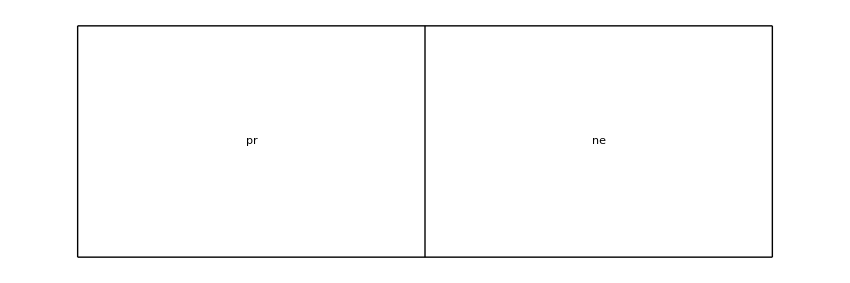
-Graphics-ge.s

```mathematica
Monitor[
Table[
Labeled[
GraphicsGrid[
Table[
Switch[consti,
(*++++++++++++++++++++++total+++++++++++++++++++++++++++++++++++++*)
 1,(*question 4 or ≥4*)
fun`graph`octet[ (*1, use format 1*)
(*rencon [consti,octet]*)
{
rencon⟦1,octet⟧*trgegm⟦consti,octet,1⟧,
rencon⟦1,octet⟧*Re[loopgegm⟦consti,octet,1⟧],
rencon⟦1,octet⟧ *(trgegm⟦consti,octet,1⟧+Re[loopgegm⟦consti,octet,1⟧]),
expfit`gegm⟦consti,octet,1⟧
},
octetnameabbr⟦octet⟧
],
(*++++++++++++++++++++++++flavor u d s+++++++++++++++++++++++++++++++++++++*)
Alternatives[2,3,4],
fun`graph`octet[ (*2-4, use format 1*)
{
rencon⟦consti,octet⟧*trgegm⟦consti,octet,1⟧,
rencon⟦consti,octet⟧*Re[loopgegm⟦consti,octet,1⟧],
rencon⟦consti,octet⟧ *(trgegm⟦consti,octet,1⟧+Re[loopgegm⟦consti,octet,1⟧])
},
octetnameabbr⟦octet⟧
],
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Alternatives[5,6,7,8,9,10,11,12,13],
fun`graph`octet`sea`valence[(*5-13, use format 2*)

Re[loopgegm⟦consti,octet,1⟧],
octetnameabbr⟦octet⟧
]
](*switch end*)
(*below,customize the graphic order*)
,{
octetgroup,{{4,5}}
}(*table level 1*)
,{octet,octetgroup}(*table level 2*)
],
Spacings->Scaled[0.01],
Frame->All,
ImageSize->850,
AspectRatio->1/3
]
(*consti label style*)
,Style[fig`geconstiname⟦consti⟧,"Subsection"],{{Top,Left}}
,Spacings->{2,2}(* labeled spacing*)
]
,{consti,4,4,1}
]
,
{octetgroup,octet}
]//TableForm
```

## fun`apply to gm

```mathematica
Monitor[
Table[
Labeled[
GraphicsGrid[
Table[
Switch[consti,(*test the indicator value*)
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
 1,(*question 4 or ≥4*)
fun`graph`octet[ (*1, use format 1*)
(*rencon [consti,octet]*)
{
rencon⟦1,octet⟧*trgegm⟦consti,octet,2⟧,
rencon⟦1,octet⟧*Re[loopgegm⟦consti,octet,2⟧],
rencon⟦1,octet⟧ *(trgegm⟦consti,octet,2⟧+Re[loopgegm⟦consti,octet,2⟧]),
expfit`gegm⟦consti,octet,2⟧
},
octetnameabbr⟦octet⟧
],
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Alternatives[2,3,4],
fun`graph`octet[ (*2-4, use format 1*)

{
rencon⟦consti,octet⟧ *trgegm⟦consti,octet,2⟧,
rencon⟦consti,octet⟧*Re[loopgegm⟦consti,octet,2⟧],
rencon⟦consti,octet⟧ *(trgegm⟦consti,octet,2⟧+Re[loopgegm⟦consti,octet,2⟧])
},
octetnameabbr⟦octet⟧
],
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Alternatives[5,6,7,8,9,10,11,12,13],
fun`graph`octet`sea`valence[(*5-13, use format 2*)

Re[loopgegm⟦consti,octet,2⟧],
octetnameabbr⟦octet⟧
]
](*switch end*)
(*below,customize the graphic order*)
,{
octetgroup,{{4,5}}
}(*table level 1*)
,{octet,octetgroup}(*table level 2*)
],
Spacings->Scaled[0.01],
Frame->All,
ImageSize->850,
AspectRatio->1/3
]
(*consti label style*)
,Style[fig`gmconstiname⟦consti⟧,"Subsection"],{{Top,Left}}
,Spacings->{2,2}(* labeled spacing*)
]
,{consti,1,1,1}
]
,
{octetgroup,octet}
]//TableForm
```

-Graphics-gm.total

gegm.ed2 nucleon perspective

## fig`octet`pers

```mathematica
fig`octet`pers=Function[{datalist,octetnameabbr},
(*+++++++++++++++++++++++++++++++++++++++plot function for tot,u,d,s,1-4+++++++++++++++++++++++++++++++++++*)
Labeled[
Plot[
datalist,
{Q2,0,2},
PlotRange->{{0,2},Full},
PlotLabels->{
Callout["Tree",Automatic,0.3,LeaderSize->{5,90°,1}],
(*only this callout usage finally worked*)
Callout["Loop",Automatic,0.8,LeaderSize->{5,45°,1}],
Callout["Total",Automatic,1.2,LeaderSize->{5,45°,1}],
Callout["Exp.",Automatic,1.6,LeaderSize->{5,90°,1}]
},(*add labels*)
ImageSize->Scaled[0.6],
AspectRatio->1/1.6,
PlotRangePadding->{Automatic,Scaled[0.15]}
]
(*label style*)
,Style[octetnameabbr,"Subsection"],{{Top,Left}}
]
];
```

## fun`apply to ge

```mathematica
fig`consti=1;
fig`octet=4;
```

```mathematica
Switch[fig`consti,
(*++++++++++++++++++++++total+++++++++++++++++++++++++++++++++++++*)
 1,(*question 4 or ≥4*)
fig`octet`pers[ (*1, use format 1*)
(*rencon [consti,octet]*)
{
rencon⟦1,fig`octet⟧*trgegm⟦fig`consti,fig`octet,1⟧,
rencon⟦1,fig`octet⟧*Re[loopgegm⟦fig`consti,fig`octet,1⟧],
rencon⟦1,fig`octet⟧ *(trgegm⟦fig`consti,fig`octet,1⟧+Re[loopgegm⟦fig`consti,fig`octet,1⟧]),
expfit`gegm⟦fig`consti,fig`octet,1⟧
},
octetnameabbr⟦fig`octet⟧
],
(*++++++++++++++++++++++++flavor u d s+++++++++++++++++++++++++++++++++++++*)
Alternatives[2,3,4],
fig`octet`pers[ (*2-4, use format 1*)
{
rencon⟦fig`consti,fig`octet⟧*trgegm⟦fig`consti,fig`octet,1⟧,
rencon⟦fig`consti,fig`octet⟧*Re[loopgegm⟦fig`consti,fig`octet,1⟧],
rencon⟦fig`consti,fig`octet⟧ *(trgegm⟦fig`consti,fig`octet,1⟧+Re[loopgegm⟦fig`consti,fig`octet,1⟧])
},
octetnameabbr⟦fig`octet⟧
],
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Alternatives[5,6,7,8,9,10,11,12,13],
fun`graph`octet`sea`valence[(*5-13, use format 2*)

Re[loopgegm⟦fig`consti,fig`octet,1⟧],
octetnameabbr⟦fig`octet⟧
]
](*switch end*)
(*below,customize the graphic order*)
```

-Graphics-pr

## Q2 table

Q2  table initial

```mathematica
(*trf1f2 is [consti,octet,treef1f2][4*8*2]*)
(*trgegm is [consti,octet,treegegem][4*8*2]*)
```

```mathematica
Once[octetcharge={
(*1*)-1,(*2*)0,(*3*)1,
(*4*)1,(*5*)0,
(*6*)-1,(*7*)0,
(*8*)0
}];
```

```mathematica
Once[octetmageton={
(*1*)−1.160,(*2*)0.60,(*3*)2.458,
(*4*)2.7928473446,(*5*)−1.9130427,
(*6*)−0.6507,(*7*)−1.250,
(*8*)−0.613
}];
```

```mathematica
Once[octet`ge`gm={
{
(*1*)-1,(*2*)0,(*3*)1,
(*4*)1,(*5*)0,
(*6*)-1,(*7*)0,
(*8*)0
},
{
(*1*)−1.160,(*2*)0.60,(*3*)2.458,
(*4*)2.7928473446,(*5*)−1.9130427,
(*6*)−0.6507,(*7*)−1.250,
(*8*)−0.613
}
}];
```

```mathematica
Once[getree=Re[trgegm⟦;;,;;,1⟧/.Q2->0]];
```

```mathematica
Once[gmtree=Re[trgegm⟦;;,;;,2⟧/.Q2->0]];
```

```mathematica
Once[gegmtree=Re[trgegm/.Q2->0]];
```

```mathematica
Once[tab`octetnameabbr=
{"term","Σm","Σ0","Σp","pr","ne","Ξm","Ξ0","Λ"}];
```

```mathematica
Once[term`name={{"tree","loop","tot","exp.","diff"},
{"tree","loop","tot","exp.","diff","per"}
}];
```

```mathematica
(*getree is [consti,octet,][4*8]*)
(*gmtree is [consti,octet,][4*8]*)
(*gegmtree is [consti,octet,treegegem][4*8*2]*)
```

```mathematica
Once[geconstiname={"Ge.all","Ge.u","Ge.d","Ge.s"}];
Once[gmconstiname={"Gm.all","Gm.u","Gm.d","Gm.s"}];
```

ge & gm

```mathematica
Dimensions/@{nugegm,loopged0,loopgmd0}
```

{{13,8,2},{13,8},{13,8}}

```mathematica
(*nugegm is [consti,octet,treegegem][13*8*2]equal loopged0 loopgdm0*)
(*{cur2ereci,cur2mreci} are ⟦consti,oct⟧[4,8]*)
```

fucoeandmrrlraw: 4 tot,u,d,s
Transpose[chpt`qfb`quench`coemass,{2,3,1}]:5u,6d,7s
Transpose[chpt`qfa`valence`coemass,{2,3,1}]:8u,9d,10s
Transpose[chpt`qfa`sea`coemass,{2,3,1}]:11u,12d,13s

## fun`Q2table`format

```mathematica
fun`Q2table`format=Function[{legendname,columnname,rowname,datalist},
Labeled[
Grid[(*grid start*)
(Prepend[(*add names row*)
MapThread[Prepend,{(*add names column*)
datalist,(*add the data to display*)
columnname(*prepend names column *)
}
]
,rowname(* prepend names  row *)
])⟦;;,{1,5,6}⟧
(*++++++++++only adopt the  proton neutron++++++++++++++++*)
,Frame->{All,All}
,Spacings->{2,2}
,Background->{None,{{None,None}}}
](*grid end*)
,legendname
,{{Top,Left}}
,LabelStyle->Directive[Red,Bold,20,FontFamily->"Times New Roman"]
]
];
```

## fun`Q2table`format apply

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
Multicolumn[(*add divider lines*)
Table[
tetable=Re[
Cancel[Chop[({loopged0,loopgmd0}⟦gegmord⟧),choplimit]]/.Q2->0(*gives loop zero term, choose loopged0 or loopgmd0*)
];
Multicolumn[
{(* paras of column need an {} *)
(*+++++++++++++++++++++++++sea-valence part  +++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
fun`Q2table`format[
{"Ge.loop.quench-sea-valence","Gm.loop.quench-sea-valence"}⟦gegmord⟧,(*legend name*)
{
"u-quench","d-quench","s-quench",
"u-valence","d-valence","s-valence",
"u-sea","d-sea","s-sea",
"u-loop.tot","d-loop.tot","s-loop.tot"
},(*column name*)
tab`octetnameabbr,(*row name*)
(*data list start*)
Join[
tetable⟦5;;13⟧,
(*add quench-sea-valence flavor contris*)
{Total[tetable⟦{5,8,11}⟧,{1}]},
(*u total 5 8 11*)
{Total[tetable⟦{6,9,12}⟧,{1}]},
(*d total 6 9 12*)
{Total[tetable⟦{7,10,13}⟧,{1}]}
(*s total 7 10 13*)
]
(*data list end*)
]
(*+++++++++++++++++++++++++sea-valence part  +++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
}
,1
],
{gegmord,1,2,1}
(*table index gegmord ge1, gm2*)
]
,2
,Spacings->4
]
```

term | pr | ne
u-quench | 0.419333 | -0.00495881
d-quench | 0.283978 | 0.138706
s-quench | 0 | 0
u-valence | 0.566648 | 0.425715
d-valence | 0.235861 | 0.756503
s-valence | 0 | 0
u-sea | -0.0453861 | 0.0495412
d-sea | -0.0495412 | 0.0453861
s-sea | 0 | 0
u-loop.tot | 0.940595 | 0.470298
d-loop.tot | 0.470298 | 0.940595
s-loop.tot | 0 | 0Ge.loop.quench-sea-valence | term | pr | ne
u-quench | 1.30648 | -1.12469
d-quench | -1.03728 | 1.36633
s-quench | 0 | 0
u-valence | 0.841525 | 0.108136
d-valence | 0.0186869 | 0.820592
s-valence | 0 | 0
u-sea | -0.28116 | -0.230723
d-sea | -0.228683 | -0.320077
s-sea | -0.0379531 | -0.0379531
u-loop.tot | 1.86685 | -1.24728
d-loop.tot | -1.24728 | 1.86685
s-loop.tot | -0.0379531 | -0.0379531Gm.loop.quench-sea-valence

## fun`Q2table`format apply 2 short version

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
Multicolumn[(*add divider lines*)
Table[
tetable=Re[
Cancel[Chop[({loopged0,loopgmd0}⟦gegmord⟧),choplimit]]/.Q2->0(*gives loop zero term, choose loopged0 or loopgmd0*)
];
Multicolumn[
{(* paras of column need an {} *)
(*+++++++++++++++++++++++++sea-valence part  +++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
fun`Q2table`format[
{"Ge.loop.quench-sea-valence","Gm.loop.quench-sea-valence"}⟦gegmord⟧,(*legend name*)
{
"u-quench","d-quench","s-quench",
"u-valence","d-valence","s-valence",
"u-sea","d-sea","s-sea",
"u-loop.tot","d-loop.tot","s-loop.tot"
},(*column name*)
tab`octetnameabbr,(*row name*)
(*data list start*)
{
(*u d s quench 5 6 7down*)
rencon⟦2⟧*tetable⟦5⟧,
rencon⟦3⟧*tetable⟦6⟧,
rencon⟦4⟧*tetable⟦7⟧,
(*u d s quench+valence in sea 8 9 10 down*)
rencon⟦2⟧*(tetable⟦5⟧+tetable⟦8⟧),
rencon⟦3⟧*(tetable⟦6⟧+tetable⟦9⟧),
rencon⟦4⟧*(tetable⟦7⟧+tetable⟦10⟧),
(*u d s sea 11 12 13 down*)
rencon⟦2⟧*tetable⟦11⟧,
rencon⟦3⟧*tetable⟦12⟧,
rencon⟦4⟧*tetable⟦13⟧,
(*quench-sea-valence summation for flavor down*)
rencon⟦2⟧*Total[tetable⟦{5,8,11}⟧,{1}],
(*u total 5 8 11*)
rencon⟦3⟧*Total[tetable⟦{6,9,12}⟧,{1}],
(*d total 6 9 12*)
rencon⟦4⟧*Total[tetable⟦{7,10,13}⟧,{1}]
(*s total 7 10 13*)
(*quench-sea-valence summation for flavor up*)
}
(*data list end*)
]
(*+++++++++++++++++++++++++sea-valence part  +++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
}
,1
],
{gegmord,1,2,1}
(*table index gegmord ge1, gm2*)
]
,2
,Spacings->4
]
```

term | pr | ne
u-quench | 0.285203 | -0.00337266
d-quench | 0.193143 | 0.0943388
s-quench | 0 | 0
u-valence | 0.6706 | 0.286171
d-valence | 0.35356 | 0.608863
s-valence | 0 | 0
u-sea | -0.0308686 | 0.0336947
d-sea | -0.0336947 | 0.0308686
s-sea | 0 | 0
u-loop.tot | 0.639731 | 0.319866
d-loop.tot | 0.319866 | 0.639731
s-loop.tot | 0 | 0Ge.loop.quench-sea-valence | term | pr | ne
u-quench | 0.888585 | -0.764943
d-quench | -0.705493 | 0.92929
s-quench | 0 | 0
u-valence | 1.46093 | -0.691396
d-valence | -0.692783 | 1.4874
s-valence | 0 | 0
u-sea | -0.191227 | -0.156923
d-sea | -0.155535 | -0.217696
s-sea | -0.0379531 | -0.0379531
u-loop.tot | 1.26971 | -0.848318
d-loop.tot | -0.848318 | 1.26971
s-loop.tot | -0.0379531 | -0.0379531Gm.loop.quench-sea-valence

## fun`Q2table`format apply.ed3

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
tab`zero`value`seavalence=Style[
Multicolumn[(*add divider lines*)
Table[
tetable=Re[
Cancel[Chop[({loopged0,loopgmd0}⟦gegmord⟧),choplimit]]/.Q2->0(*gives loop zero term, choose loopged0 or loopgmd0*)
];
Multicolumn[
{(* paras of column need an {} *)
(*+++++++++++++++++++++++++sea-valence part  +++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
fun`Q2table`format[
{"Ge.loop.quench-sea-valence","Gm.loop.quench-sea-valence"}⟦gegmord⟧,(*legend name*)
{
"u-quench","d-quench","s-quench",
"u-di-valence","d-di-valence","s-di-valence",
"u-tot-valence","d-tot-valence","s-tot-valence",
"u-sea","d-sea","s-sea",
"u-loop.tot","d-loop.tot","s-loop.tot"
},(*column name*)
tab`octetnameabbr,(*row name*)
(*data list start*)
{
(*u d s quench 5 6 7down*)
(*rencon⟦2⟧**)tetable⟦5⟧,
(*rencon⟦3⟧**)tetable⟦6⟧,
(*rencon⟦4⟧**)tetable⟦7⟧,
(*u d s disconnected insert valence in sea 8 9 10 down*)
(*rencon⟦2⟧**)tetable⟦8⟧,
(*rencon⟦3⟧**)tetable⟦9⟧,
(*rencon⟦4⟧**)tetable⟦10⟧,
(*u d s quench+di-valence in sea 8 9 10 down*)
(*rencon⟦2⟧**)(tetable⟦5⟧+tetable⟦8⟧),
(*rencon⟦3⟧**)(tetable⟦6⟧+tetable⟦9⟧),
(*rencon⟦4⟧**)(tetable⟦7⟧+tetable⟦10⟧),
(*u d s sea 11 12 13 down*)
(*rencon⟦2⟧**)tetable⟦11⟧,
(*rencon⟦3⟧**)tetable⟦12⟧,
(*rencon⟦4⟧**)tetable⟦13⟧,
(*quench-sea-valence summation for flavor down*)
(*rencon⟦2⟧**)Total[tetable⟦{5,8,11}⟧,{1}],
(*u total 5 8 11*)
(*rencon⟦3⟧**)Total[tetable⟦{6,9,12}⟧,{1}],
(*d total 6 9 12*)
(*rencon⟦4⟧**)Total[tetable⟦{7,10,13}⟧,{1}]
(*s total 7 10 13*)
(*quench-sea-valence summation for flavor up*)
}
(*data list end*)
]
(*+++++++++++++++++++++++++sea-valence part  +++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
}
,1
],
{gegmord,1,2,1}
(*table index gegmord ge1, gm2*)
]
,2
,Spacings->4
]
,FontSize->8
]
```

term | pr | ne
u-quench | 0.276992 | 0.138496
d-quench | 0.138496 | 0.276992
s-quench | 0 | 0
u-di-valence | 0.43081 | 0.215405
d-di-valence | 0.215405 | 0.43081
s-di-valence | 0 | 0
u-tot-valence | 0.707802 | 0.353901
d-tot-valence | 0.353901 | 0.707802
s-tot-valence | 0 | 0
u-sea | 0 | 0
d-sea | 0 | 0
s-sea | 0 | 0
u-loop.tot | 0.707802 | 0.353901
d-loop.tot | 0.353901 | 0.707802
s-loop.tot | 0 | 0Ge.loop.quench-sea-valence | term | pr | ne
u-quench | 0.979401 | -0.646383
d-quench | -0.616595 | 1.00919
s-quench | 0 | 0
u-di-valence | 0.602109 | -0.0706793
d-di-valence | -0.100467 | 0.572321
s-di-valence | 0 | 0
u-tot-valence | 1.58151 | -0.717062
d-tot-valence | -0.717062 | 1.58151
s-tot-valence | 0 | 0
u-sea | -0.14835 | -0.322946
d-sea | -0.322946 | -0.14835
s-sea | -0.0267239 | -0.0267239
u-loop.tot | 1.43316 | -1.04001
d-loop.tot | -1.04001 | 1.43316
s-loop.tot | -0.0267239 | -0.0267239Gm.loop.quench-sea-valence

```mathematica
Export[
"C:\\Users\\Tom\\Desktop\\octet.paper.ed4\\zero.value.sea-valence.eps",
tab`zero`value`seavalence
]
```

C:\Users\Tom\Desktop\octet.paper.ed4\zero.value.sea-valence.eps

consistency test

```mathematica
octetmageton`c1c2c3={
(*1 Σ*)-1+1/3 (c1-3 c2),c1/3,1+1/3 (c1+3 c2),
(*4 N*)1+1/3 (c1+3 c2),-(2 c1)/3,
(*6 Ξ*)-1+1/3 (c1-3 c2),-(2 c1)/3,
(*4 Λ*)-c1/3
};(*described by μu && μs (substitute with c1 c2 c3)*)
rencon⟦1⟧*gmtree⟦1⟧
rencon⟦1⟧*octetmageton`c1c2c3/.baselist2
```

{-0.758399,0.489858,1.73811,1.655,-0.932866,-0.835216,-1.07895,-0.505588}

{-0.758399,0.489858,1.73811,1.655,-0.932866,-0.835216,-1.07895,-0.505588}

## perspective

```mathematica
Once[each`nuff1=Table[0,{series,1,3,1},{constituent,1,4,1}]];
Once[each`nuff2=Table[0,{series,1,3,1},{constituent,1,4,1}]];
Monitor[
Table[
(each`nuff1⟦series,constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,diag,oct,coe⟧*ff1`series⟦series,diag⟧
)/.baselist⟦oct⟧
)/.fumass⟦constituent,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{3}]);
(each`nuff2⟦series,constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,diag,oct,coe⟧*ff2`series⟦series,diag⟧
)/.baselist⟦oct⟧
)/.fumass⟦constituent,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{3}]);
,{series,1,3,1}(*series order 0 1 2*)
,{constituent,1,4,1}(*consti u d s *)
];
,{series,constituent,oct,diag,coe}
]//AbsoluteTiming
(*each`nuff1,each`nuff2 is 3*4*8*11 [order*flavor*octet*diagram]*)
```

{342.349,Null}

```mathematica
each`nugegm=Transpose[(* 8*2*3*4*11 transpose into 2*3*4*8*11 *)
Table[
-1/(16 π^2){
each`nuff1⟦;;,;;,i,;;⟧-Q2/(4 constmo⟦i⟧^2)each`nuff2⟦;;,;;,i,;;⟧,
each`nuff1⟦;;,;;,i,;;⟧+each`nuff2⟦;;,;;,i,;;⟧
},
{i,1,8,1}]
,{4,1,2,3,5}
];//AbsoluteTiming
```

{0.0129227,Null}

```mathematica
each`nuff1//Dimensions
each`nuff2//Dimensions
each`nugegm//Dimensions
```

{3,4,8,11}

{3,4,8,11}

{2,3,4,8,11}

loop derivative coefficient

loopged2⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧/(-4loopged1⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧)-loopged1⟦flavor`oct⟦1⟧,flavor`oct⟦2⟧⟧

fch' s results

loopd1:a+b+d+e≈0, f+g=sign[+], h+i+m+n=sign[-], o+p=sign[+]

reciprocal

{loopged0,cur2ereci}
{loopgmd0,cur2mreci}

nugegm⟦f1f2,series,flavor,oct⟧2*3*13*8

```mathematica
({
{each`loopged0,each`loopged1,each`loopged2},
{each`loopgmd0,each`loopgmd1,each`loopgmd2}
}=Simplify[each`nugegm/.Q2->0]);//AbsoluteTiming
(*{loopged0,loopged1,loopgmd0,loopgmd1} ⟦consti*oct*diagram⟧[4*8*11]*)
```

{0.0159752,Null}

```mathematica
fun`looptable[each1_,each2_]:=Append[each1,Total[each2*
{
1,1,
1,(*3*)
1,1,1,1,
1,1,(*8,9*)
1,1
}
]
]
fun`looptable`disply[consti_,octet_]:=TableForm[
Transpose[
Chop[{
fun`looptable[each`loopged0⟦consti,octet⟧,each`loopged0⟦consti,octet⟧],
fun`looptable[each`loopged1⟦consti,octet⟧,each`loopged1⟦consti,octet⟧],
fun`looptable[each`loopged2⟦consti,octet⟧,each`loopged2⟦consti,octet⟧]
},
choplimit
]
],
TableHeadings->{
Append[diagname,"tot."],
{"loopd0","loopd1","loopd2"}
}
]
```

```mathematica
fun`looptable`disply[1,4](*s in pr*)
fun`looptable`disply[2,4](*d in Σp*)
fun`looptable`disply[3,4](*d in Σp*)
fun`looptable`disply[4,4](*d in Σp*)
```

| loopd0 | loopd1 | loopd2
1a | 0.0694516 | -0.502309 | 2.69831
2b | 0.119781 | -0.333588 | 0.651748
3c | 0 | 0.0429939 | -0.118904
4de | 0.120965 | -0.29868 | 0.55311
5fg | 0.0625687 | -0.227419 | 0.528792
6h | -0.00477466 | 0.0414448 | -0.184464
7i | 0.126303 | -0.324016 | 0.608497
8j | 0 | -0.00276958 | 0.0088162
9kl | 0 | 0.0682035 | -0.170318
10mn | -0.017217 | 0.0425111 | -0.0787243
11op | -0.0067802 | 0.0266248 | -0.0628238
tot. | 0.470298 | -1.57543 | 4.71444

| loopd0 | loopd1 | loopd2
1a | 0.0694516 | -0.502309 | 2.69831
2b | 0.492547 | -1.36975 | 2.67419
3c | 0 | 0.0370472 | -0.102424
4de | 0.120965 | -0.29868 | 0.55311
5fg | 0.0625687 | -0.227419 | 0.528792
6h | -0.00477466 | 0.0414448 | -0.184464
7i | 0.223834 | -0.574211 | 1.07835
8j | 0 | -0.00487702 | 0.0155331
9kl | 0 | 0.0682035 | -0.170318
10mn | -0.017217 | 0.0425111 | -0.0787243
11op | -0.0067802 | 0.0266248 | -0.0628238
tot. | 0.940595 | -2.86178 | 7.20673

| loopd0 | loopd1 | loopd2
1a | -0.0672511 | 0.493223 | -2.67572
2b | 0.603232 | -1.67893 | 3.27912
3c | 0 | -0.0499499 | 0.138821
4de | -0.104481 | 0.257979 | -0.477739
5fg | -0.0587327 | 0.214587 | -0.501056
6h | 0.00532704 | -0.0448005 | 0.193875
7i | 0.0631516 | -0.162008 | 0.304248
8j | 0 | -0.00138479 | 0.0044081
9kl | 0 | -0.0669034 | 0.167109
10mn | 0.0210087 | -0.0518734 | 0.0960618
11op | 0.00804396 | -0.0316613 | 0.0741463
tot. | 0.470298 | -1.00348 | 0.292939

| loopd0 | loopd1 | loopd2
1a | -0.00220049 | 0.00908644 | -0.02259
2b | 0.0225202 | -0.0597997 | 0.114012
3c | 0 | -0.00493748 | 0.0130423
4de | -0.0164837 | 0.0407006 | -0.0753714
5fg | -0.00383594 | 0.0128319 | -0.0277366
6h | -0.000552378 | 0.00335563 | -0.00941108
7i | 0.00560785 | -0.0143659 | 0.0269509
8j | 0 | -0.0000604912 | 0.000209504
9kl | 0 | -0.00130013 | 0.00320851
10mn | -0.00379172 | 0.00936227 | -0.0173375
11op | -0.00126375 | 0.00503653 | -0.0113225
tot. | 0 | 0.00620777 | -0.0228064

```mathematica
-1.4670032382027212
```

```mathematica
-2.7614113215630844
```

```mathematica
-1.1217225998584475
```

```mathematica
-0.00009032865955852995
```

```mathematica
2/3*(-2.7614113215630844)-1/3(-1.1217225998584475)-1/3(-0.00009032865955852995)
```

-1.467

sasdfsdaf

```mathematica
fun`looptable`disply[2,1](*u in Ξ0*)
fun`looptable`disply[3,3](*u in Ξ0*)
```

| loopd0 | loopd1 | loopd2
1a | -0.0638834 | 0.516414 | -3.50479
2b | 0.177522 | -0.484024 | 0.935016
3c | 0 | -0.0362657 | 0.0973854
4de | -0.057466 | 0.141891 | -0.262762
5fg | -0.0561723 | 0.204726 | -0.478251
6h | -0.00421838 | 0.0262981 | -0.0989083
7i | 0.0233787 | -0.0600244 | 0.112716
8j | 0 | -0.000296133 | 0.000970677
9kl | 0 | -0.008403 | 0.0215675
10mn | -0.0120411 | 0.0297312 | -0.0550578
11op | -0.00711918 | 0.0195688 | -0.0398945
tot. | 0 | 0.349616 | -3.27201

| loopd0 | loopd1 | loopd2
1a | -0.0638834 | 0.516414 | -3.50479
2b | 0.177522 | -0.484024 | 0.935016
3c | 0 | -0.0362657 | 0.0973854
4de | -0.057466 | 0.141891 | -0.262762
5fg | -0.0561723 | 0.204726 | -0.478251
6h | -0.00421838 | 0.0262981 | -0.0989083
7i | 0.0233787 | -0.0600244 | 0.112716
8j | 0 | -0.000296133 | 0.000970677
9kl | 0 | -0.008403 | 0.0215675
10mn | -0.0120411 | 0.0297312 | -0.0550578
11op | -0.00711918 | 0.0195688 | -0.0398945
tot. | 0 | 0.349616 | -3.27201

```mathematica
fun`looptable`disply[4,1](*u in Ξ0*)
fun`looptable`disply[3,6](*u in Ξ0*)
```

| loopd0 | loopd1 | loopd2
1a | -0.00535709 | 0.0210388 | -0.05047
2b | 0.354553 | -0.952191 | 1.82556
3c | 0 | 0.00351122 | -0.00776756
4de | -0.023574 | 0.0582075 | -0.107792
5fg | -0.010911 | 0.0355224 | -0.0757238
6h | 0.00709681 | -0.0326542 | 0.0848189
7i | 0.0411571 | -0.104617 | 0.195761
8j | 0 | -0.000708006 | 0.00208299
9kl | 0 | -0.0294522 | 0.073694
10mn | 0.0225319 | -0.0556343 | 0.103027
11op | 0.0144918 | -0.0343911 | 0.0646757
tot. | 0.399988 | -1.09137 | 2.10786

| loopd0 | loopd1 | loopd2
1a | -0.0185803 | 0.0657386 | -0.0933097
2b | 0.289413 | -0.774592 | 1.48307
3c | 0 | -0.0144513 | 0.0389863
4de | -0.0347245 | 0.0857394 | -0.158777
5fg | -0.0356485 | 0.115334 | -0.244755
6h | 0.00447232 | -0.0335423 | 0.141698
7i | 0.0464344 | -0.118311 | 0.22154
8j | 0 | -0.000585972 | 0.00177046
9kl | 0 | -0.0197346 | 0.0499709
10mn | 0.0131542 | -0.0324795 | 0.0601471
11op | 0.00670691 | -0.0232468 | 0.0513719
tot. | 0.271228 | -0.750131 | 1.55171

```mathematica
fun`looptable`disply[3,5]
fun`looptable`disply[4,7](*s in Ξ0*)
```

| loopd0 | loopd1 | loopd2
1a | 0.0694516 | -0.502309 | 2.69831
2b | 0.492547 | -1.36975 | 2.67419
3c | 0 | 0.0370472 | -0.102424
4de | 0.120965 | -0.29868 | 0.55311
5fg | 0.0625687 | -0.227419 | 0.528792
6h | -0.00477466 | 0.0414448 | -0.184464
7i | 0.223834 | -0.574211 | 1.07835
8j | 0 | -0.00487702 | 0.0155331
9kl | 0 | 0.0682035 | -0.170318
10mn | -0.017217 | 0.0425111 | -0.0787243
11op | -0.0067802 | 0.0266248 | -0.0628238
tot. | 0.940595 | -2.76141 | 6.94952

| loopd0 | loopd1 | loopd2
1a | 0.0353807 | -0.14646 | 0.369415
2b | 0.24329 | -0.648882 | 1.24019
3c | 0 | 0.0191139 | -0.0519948
4de | 0.060041 | -0.148249 | 0.274536
5fg | 0.0622078 | -0.203657 | 0.436669
6h | 0.000766021 | -0.00269663 | 0.00638649
7i | 0.139698 | -0.352946 | 0.658985
8j | 0 | -0.00240035 | 0.00673972
9kl | 0 | 0.0251683 | -0.063541
10mn | -0.000195239 | 0.000482071 | -0.000892725
11op | 0.001267 | -0.00039452 | -0.00159443
tot. | 0.542455 | -1.46092 | 2.87489